```mathematica
Integrate[((cx n0)/(2 π R T)^(3/2))Exp[-((cx^2+cy^2+cz^2)/(2 R T))],{cx,0,∞},{cy,-∞,∞},{cz,-∞,∞},Assumptions->{R>0, T>0}]
```

(n0 √(R T))/(√(2 π))

```mathematica
π r^2 dt ((n0 √((kb/m) T))/(√(2 π)))/.n0->6.02*10^12/.T->273/.kb->1.38064852*10^-16/.m->4*10^-23/.dt->5*10^-11/.r->2.5*10^-5
```

0.00723768

```mathematica
40000.0*dt/.dt->5*10^-11
```

2.×10^-6

```mathematica
π r^2 h /.r->2.5*10^-5/.h->0.5*10^-5 /.n0->6.02*10^12
```

9.81748×10^-15

```mathematica
Solve[{vpin mp+vgin mg == vpout mp+vgout mg,vpin^2 mp+vgin^2 mg == vpout^2 mp+vgout^2 mg},{vgout,vpout}]
```

{{vgout→vgin,vpout→vpin},{vgout→(mg vgin-mp vgin+2 mp vpin)/(mg+mp),vpout→(2 mg vgin-mg vpin+mp vpin)/(mg+mp)}}

```mathematica
N[{vgout->(mg vgin-mp vgin+2 mp vpin)/(mg+mp),vpout->(2 mg vgin-mg vpin+mp vpin)/(mg+mp)}/.mp->4.0*10^-23/.vpin->15968/.vgin->0/.+mg->(23.8*10^-7*π r^2)/.r->2.5*10^-5,50]
```

{vgout→0.000273359,vpout→-15968.}

```mathematica
(23.8*10^-7*π r^2)/.r->2.5*10^-5
```

4.67312×10^-15

```mathematica
80
```

```mathematica
Solve[2 π 14*10^6==(c 2.4048)/(2.5*10^-5),c]
```

{{c→914.469}}

```mathematica
5.0*10^-4
```

0.0005

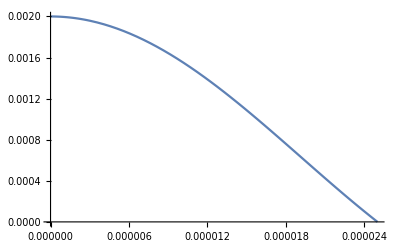

```mathematica
Plot[2*10^-3 BesselJ[0,r/(2.5*10^-5)2.4048],{r,0,2.5*10^-5}]
```

```mathematica
23.8*10^-7 2 π Integrate[3.834534618379*10^-4* BesselJ[0,r/(2.5*10^-5)2.4048]r,{r,0,2.5*10^-5}]
```

7.73688×10^-19

```mathematica
2*4.0*10^-23*3071.9688298885003
```

2.45758×10^-19

```mathematica
7.736881098317622*^-19/2.4575750639108005*^-19
```

3.14818

```mathematica
2 π Integrate[BesselJ[0,r/a 2.4048]r,{r,0,a}]
```

2 (0.+0.215882 a^2) π